# Лабораторная работа 3.

Шпак Андрей, 3 курс, 5 группа.

## Задание 1. Математический маятник под действием силы тяжести без учета сопротивления среды.

```mathematica
g=QuantityMagnitude@WolframAlpha["Gravitational acceleration value", {{"Value",1},"QuantityData"}]
```

9.807

### Задание 1.1 (Фазовый портрет)

```mathematica
(*Фото*)
```

```mathematica
l=1;
```

```mathematica
legend=LineLegend[{Red,Blue,Green,Yellow},{"Сепаратриса","Вращательное движение","Колебательное движение","Нижнее положение равновесия"}];
```

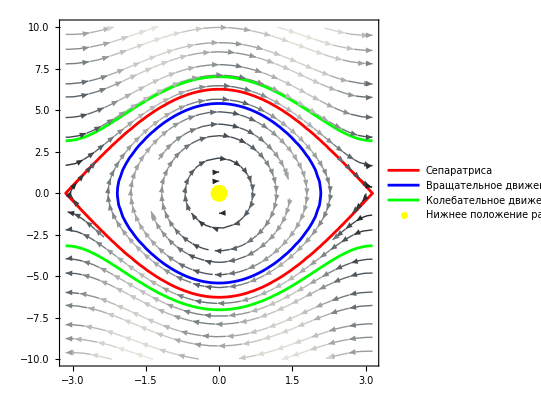

```mathematica
Show[StreamPlot[{ω,-g/l*Sin[α]},{α,-Pi,Pi},{ω,-10,10},StreamColorFunction->"GrayTones"],ContourPlot[ω^2/2-g/l*Cos[α]==g/l,{α,-Pi,Pi},{ω,-10,10},ContourStyle->{Red,Thick},PlotLegends->{"Сепаратриса"}],
ContourPlot[ω^2/2-g/l*Cos[α]+5==g/l,{α,-Pi,Pi},{ω,-10,10},ContourStyle->{Blue,Thick},PlotLegends->{"Вращательное движение"}],
ContourPlot[ω^2/2-g/l*Cos[α]-5==g/l,{α,-Pi,Pi},{ω,-10,10},ContourStyle->{Green,Thick},PlotLegends->{"Колебательное движение"}],
ListPlot[{{0,0}},PlotStyle->{PointSize[0.03],Yellow},PlotLegends->{"Нижнее положение равновесия"}],PlotRange->All,PlotLegends->Placed[{"Сепаратриса","Вращательное движение","Колебательное движение","Нижнее положение равновесия"},{Right,Top}]]
```

### Задание 1.2 (Динамическая визуализация)

Колебательные движения.

```mathematica
Manipulate[Animate[Graphics[{
Line[{{0,0},{l*Sin[First@(α[time]/.NDSolve[{α''[t]+g/l Sin[α[t]]==0,α[0]==α0,α'[0]==ω0},α,{t,0,30}])],-l*Cos[First@(α[time]/.NDSolve[{α''[t]+g/l Sin[α[t]]==0,α[0]==α0,α'[0]==ω0},α,{t,0,30}])]}}],PointSize@0.01,Point[{0,0}],PointSize@0.03,Red,Point[{l*Sin[First@(α[time]/.NDSolve[{α''[t]+g/l Sin[α[t]]==0,α[0]==α0,α'[0]==ω0},α,{t,0,30}])],-l*Cos[First@(α[time]/.NDSolve[{α''[t]+g/l Sin[α[t]]==0,α[0]==α0,α'[0]==ω0},α,{t,0,30}])]}],
Black,Text[If[And[α0==0,ω0==0],"Нижнее положение равновесия",If[And[α0==Pi,ω0==0],"Сепаратриса",If[-g/l<=ω0^2/2-g/l*Cos[α0]<g/l,"Колебательные движения",If[ω0^2/2-g/l*Cos[α0]>g/l,"Вращательные движения"]]]],{0,-5}]},PlotRange->{{-6,6},{-6,6}}],{time,0,30},DefaultDuration->100],{α0,0,Pi},{ω0,0,10},{l,1,5},Button["Нижнее положение равновесия",{α0=0,ω0=0}],
Button["Колебательные движения",{α0=Pi/4,ω0=3}],Button["Вращательные движения",{α0=Pi/2,ω0=6}],Button["Сепаратриса",{α0=Pi,ω0=0}]]
```